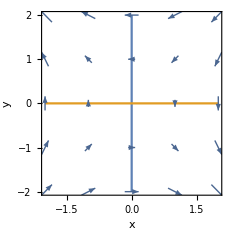

```mathematica
p0 = ContourPlot[{x==0,y==0},{x,-2,2},{y,-2,2},FrameLabel->{x,y},LabelStyle->Medium];
p1 = VectorPlot[{-y,-x},{x,-2,2},{y,-2,2},VectorPoints->5,VectorScale->Medium];
Export["pset03_519.png",Show[p0,p1]]
```